#### Notes

Maybe we can test random weights for some number of attempts then skip to next if none are found. This random search would reduce memory complexity of the algorithm. 
		First: Test random weights to reduce Graph List
	 	Second: Complete Test of all weights
	 	Third: ?
	
	Understanding the relationships between graphs would be nice. We could test the graphs in order of inclusion as a subgraph. So Construct a Poset of the graphs where the order is by inclusion as isomorphic subgraphs ( Not sure if this actually leads to a Poset structure but the idea is still there). Then perform tests according to the ordering.

#### Code

```mathematica
(* Brute force construction of all Graphs on n vertices up to Isomorphism*)
allEdges[n_]:=Flatten[Table[UndirectedEdge[i,j],{i,1,n},{j,i+1,n}]];
allConnected[n_]:=Select[Map[Graph[Range[n],#,VertexLabels->Automatic]&,Subsets[allEdges[n]]],ConnectedGraphQ];
allConnectedUpToIso[n_]:=DeleteDuplicatesBy[allConnected[n],CanonicalGraph];

(*Helper Functions*)
PerfectDistanceQ[G_,w_]:=Union@*Flatten@*Round@GraphDistanceMatrix[Graph[G,EdgeWeight->w]] == Range[0,Binomial[VertexCount[G],2]];
WeightsList[G_]:=Flatten[Permutations[#]&/@Select[Subsets[Range[Binomial[VertexCount[G],2]],{EdgeCount[G]}],MemberQ[#,1]&&MemberQ[#,2]&],1] 
WeightSets[Vn_,En_]:=WeightSets[Vn,En]=Select[Subsets[Range[Binomial[Vn,2]],{En}],MemberQ[#,1]&&MemberQ[#,2]&] ;
TotalWeightings[G_] := EdgeCount[G]!Binomial[Binomial[VertexCount[G],2]-2,EdgeCount[G]-2];
StatusGraph[GraphList_,NPDG_,MPDG_]:=Module[{G},G =ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,GraphList]; HighlightGraph[G,{Style[NPDG,Red],Style[VertexOutComponent[G,MPDG],Green]},GraphLayout->"LayeredDigraphEmbedding",VertexLabels->MapIndexed[#->Placed[{VertexList[G][[#2[[1]]]]},{Tooltip}]&,VertexList[G]]]];
TimeToCheckPerWeight =0.000021175520621353957;
DistributeDefinitions[PerfectDistanceQ];
statusP = 0;
SetSharedVariable[statusP]
```

```mathematica
(*Temp1 = TopologicalSort[ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,vertex6]];*)
(*SubGraphMatrix = AdjacencyMatrix[ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,vertex6]];*)
vertex5 = allConnectedUpToIso[5];
vertex6 = SortBy[Import["/Users/alexanderhabib/Desktop/Graphs/connected_graphs/n_6/graph6c.g6"],EdgeCount[#]&];
```

```mathematica
Test = Import["/Users/alexanderhabib/MPDG7_Incomplete.mx"];
```

```mathematica
Temp1 = TopologicalSort[ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,vertex5]];
```

1.

1.

1.

0.410714

1.

0.

0.285714

0.178571

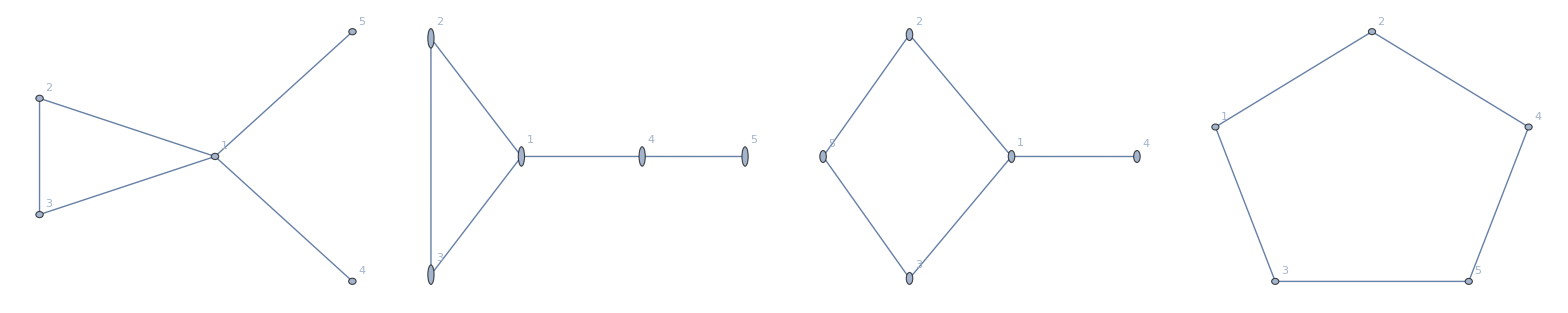
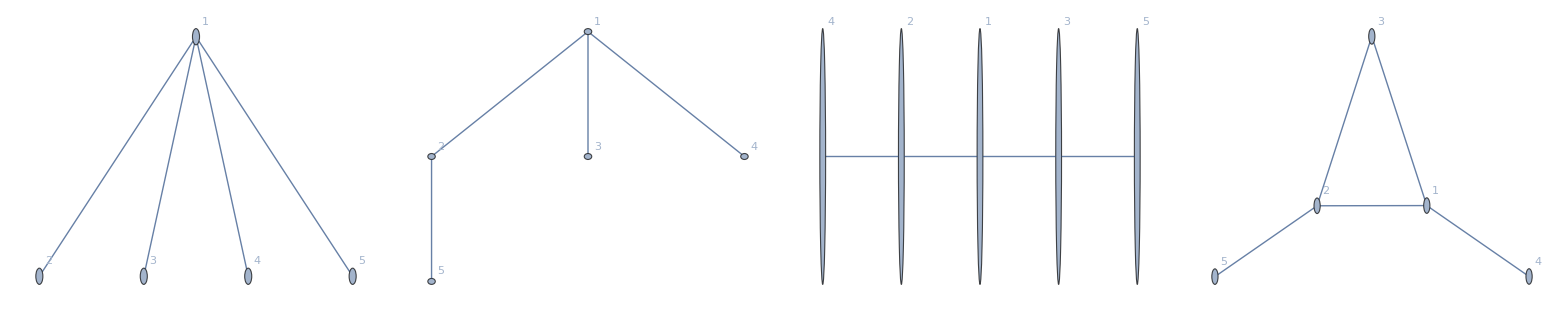
Time To Compute:	00:00:00TimeObject[{0,0,0.32262},Instant] and 322.62ms
Minimal Perfect Distance Graphs(4): 
-Graphics-
Not Perfect Distance Graphs(4): 
-Graphics-

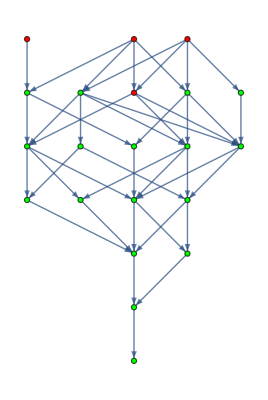

```mathematica
GraphList =vertex5;
LStart = Length[GraphList];
lenGL=LStart;
MinimalPerfectDistanceGraphs = {}; NotPerfectDistanceGraphs = {};

P1=ProgressIndicator[Dynamic[(LStart-lenGL)/LStart]]
P2=ProgressIndicator[Dynamic[status/lenW]]

TotalTime = AbsoluteTiming[
While[Length[GraphList]>0,
G = First[GraphList];
GraphList = Delete[GraphList,1];

W = WeightSets[VertexCount[G],EdgeCount[G]];

status=0;
lenW = Length[W];

PDGQ =Catch[Do[
WL = Permutations[Wi];ResWi =Catch[Do[If[PerfectDistanceQ[G,w],Throw[True]],{w,WL}]];If[ResWi===True,Throw[ResWi]];status++,{Wi,W}]];
Print[N[status/lenW]];

If[PDGQ===True,
AppendTo[MinimalPerfectDistanceGraphs,G];GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[G,#]]&];
,AppendTo[NotPerfectDistanceGraphs,G];
];
lenGL = Length[GraphList];
];
][[1]];

Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Minimal Perfect Distance Graphs(",Length[MinimalPerfectDistanceGraphs],"): \n",TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row],"\n",
"Not Perfect Distance Graphs(",Length[NotPerfectDistanceGraphs],"): \n",
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
]
StatusGraph[vertex5,NotPerfectDistanceGraphs,MinimalPerfectDistanceGraphs]
```

```mathematica
LaunchKernels[4];
```

```mathematica
vertex5=allConnectedUpToIso[5];
```

```mathematica
GraphList =vertex5;
LStart = Length[GraphList];
lenGL = Length[GraphList];
MinimalPerfectDistanceGraphs = {}; NotPerfectDistanceGraphs = {};

P1=ProgressIndicator[Dynamic[(LStart-lenGL)/LStart]]
P2=ProgressIndicator[Dynamic[statusP/lenW]]
Clear[lock];

TotalTime = AbsoluteTiming[
While[Length[GraphList]>0,
G = First[GraphList];
GraphList = Delete[GraphList,1];

W = WeightSets[VertexCount[G],EdgeCount[G]];

statusP=0;
SetSharedVariable[statusP];
lenW = Length[W];

DistributeDefinitions[G];
PDGQ=ParallelTry[(statusP++;If[Catch[Do[If[PerfectDistanceQ[G,w],Throw[True]],{w,Permutations[#]}]]===True,True,$Failed])&,W,DistributedContexts->None];

If[PDGQ===True,
AppendTo[MinimalPerfectDistanceGraphs,G];GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[G,#]]&];
,AppendTo[NotPerfectDistanceGraphs,G];
];
lenGL = Length[GraphList];
];
][[1]];

Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Minimal Perfect Distance Graphs(",Length[MinimalPerfectDistanceGraphs],"): \n",TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row],"\n",
"Not Perfect Distance Graphs(",Length[NotPerfectDistanceGraphs],"): \n",
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
]
```

```mathematica
vertex5 = allConnectedUpToIso[5];
```

```mathematica
GraphList =vertex5;
LStart = Length[GraphList];
lenGL = Length[GraphList];
MinimalPerfectDistanceGraphs = {}; NotPerfectDistanceGraphs = {};

P1=ProgressIndicator[Dynamic[(LStart-lenGL)/LStart]]
P2=ProgressIndicator[Dynamic[statusP/lenW]]
Clear[lockMPDG];
Clear[lockNPDG];
Clear[lockGL];

TotalTime = AbsoluteTiming[
ParallelDo[
(*CriticalSection[lockGL,G = First[GraphList];GraphList = Delete[GraphList,1]];*)

W = WeightSets[VertexCount[G],EdgeCount[G]];

statusP=0;
SetSharedVariable[statusP];
lenW = Length[W];

PDGQ=Catch[Do[
WL = Permutations[Wi];ResWi =Catch[Do[If[PerfectDistanceQ[G,w],Throw[True]],{w,WL}]];If[ResWi===True,Throw[ResWi]];status++,{Wi,W}]];

If[PDGQ===True,
CriticalSection[lockMPDG,AppendTo[MinimalPerfectDistanceGraphs,G]];(*CriticalSection[lockGL,GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[G,#]]&]]*);
,CriticalSection[lockNPDG,AppendTo[NotPerfectDistanceGraphs,G]];
];
,{G,GraphList}];
][[1]];

Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Minimal Perfect Distance Graphs(",Length[MinimalPerfectDistanceGraphs],"): \n",TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row],"\n",
"Not Perfect Distance Graphs(",Length[NotPerfectDistanceGraphs],"): \n",
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
]
```

```mathematica
StatusGraph[GraphList_,NPDG_,MPDG_]:=Module[{G},G =ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,GraphList]; HighlightGraph[G,{Style[NPDG,Red],Style[VertexOutComponent[G,MPDG,Green]]},GraphLayout->"LayeredDigraphEmbedding",VertexLabels->MapIndexed[#->Placed[{VertexList[G][[#2[[1]]]]},{Tooltip}]&,VertexList[G]]]]
```